# Get Intensities from Crops Max Intensity, Disk&Donut, Gaussian

## Executables (Adjust Input, then Shift + Enter to execute all)

## Input

### Initialize Functions

#### 6. MyBandPass

Unit Test

```mathematica
MyBandPass::usage="MyBandPass[img, {lo, hi}] outputs the input image after it has been bandpass filtered such that objects between the size of lo and hi (in pixels) are accentuated.
Inputs
1. img: an image 
2. lo: the lower limit on the size of objects to be accentuated 
3. hi: the upper limit on the size of objects to be accentuated 
";
MyBandPass[img_,{lo_,hi_}]:=Module[{imgb,imgc},
imgb=ImageConvolve[img,GaussianMatrix[{hi,lo}]];
(*imgc=ImageConvolve[img,BoxMatrix[hi]/(2 hi+1)^2];*)
imgc=ImageConvolve[img,DiskMatrix[hi]/(Plus@@Plus@@DiskMatrix[hi])];
ImageSubtract[imgb,imgc]
]
```

#### 6 1/2. MyChooseCenterSpot

Unit test:

```mathematica
test = MyFindParticlesInCrop[-Graphics-,{1,10},1,0.2,{1,100}]
test2 = MyFindParticlesInCrop[-Graphics-,{1,10},1,0.2,{1,100}]
MyChooseCenterSpot[test,myPadSize]
MyChooseCenterSpot[test2,myPadSize]
```

{{{2.59487,6.19683},0.294233,0.354955,6.72706}}

{{{7.42789,5.54785},0.03705,0.299062,6.65719}}

{{{2.59487,6.19683},0.294233,0.354955,6.72706}}

{{{7.42789,5.54785},0.03705,0.299062,6.65719}}

```mathematica
MyChooseCenterSpot::usage="MyChooseCenterSpot[myout,mypadsize] reads in a line on the particle finder output, and if there are 2 or more spots detected in the same channel crop then it selects the spot nearest to the center of the crop. 
Inputs
1. myout: line of particle finder output
2. mypad: size of the pad of the crop

";
```

```mathematica
MyChooseCenterSpot[test_,mypad_]:= Module[{padcent},
If[Length@test>1, 
padcent =  {mypad+.5,mypad+.5};
minED = Nearest[test[[All,1]],padcent]; (*minED is the nearest spot coordianates*)
Select[test,{#[[1]]}== minED&],
test
]]
```

#### 7. MyFindParticlesInCrop

Unit test:

```mathematica
test = MyFindParticlesInCrop[-Graphics-,{1,10},1,0.2,{1,100}]
test2 = MyFindParticlesInCrop[-Graphics-,{1,10},1,0.2,{1,100}]
test3 = MyFindParticlesInCrop[-Graphics-,{1,10},1,0.2,{1,100}]
```

{{{2.59487,6.19683},0.294233,0.354955,6.72706}}

{{{7.42789,5.54785},0.03705,0.299062,6.65719}}

{{{NaN,NaN},NaN,NaN,NaN}}

```mathematica
(ImageDimensions [-Graphics-] [[1]]  -1)/2
```

5

```mathematica
MyFindParticlesInCrop::usage="MyFindParticlesInCrop[img, {lo, hi}, max, th, {small, large}] outputs the input image after it has been bandpass filtered such that objects between the size of lo and hi (in pixels) are accentuated.
Inputs
1. img: an image (ONE crop, one channel only, ex: 
2. lo: the lower limit on the size of objects to be accentuated 
3. hi: the upper limit on the size of objects to be accentuated 
4. th: the threshold
5. small: the lower limit on the count of pixels after binarization
6. large: the upper limit on the count of pixels after binarization
7. pad: the pad size of the crop in pixels

";
(*MyFindParticlesInCrop[img_,{lo_,hi_},th_,{small_,large_}]:=Module[{imgb,imgc,pos,myout},
imgb=MyBandPass[img,{lo,hi}]//ImageAdjust;
imgc=SelectComponents[Binarize[imgb, th],{"Count","AdjacentBorderCount"},small<#1<large&&#2==0&];
myout=ComponentMeasurements[ImageMultiply[img,imgc],{"Count","Centroid","Elongation","IntensityCentroid","Mean","Total","MinIntensity", "MaxIntensity","TotalIntensity"},All,"Dataset"];
{myout,img//ImageAdjust,imgb//ImageAdjust,imgc//ImageAdjust}
]*)
```

```mathematica
(* MY PAD SIZE ADD TO INPUTS*)
```

```mathematica
MyFindParticlesInCrop[img_,{lo_,hi_},max_,th_,{small_,large_}]:=Module[{imgb,imgc,pad, pos},
imgb=MyBandPass[img,{lo,hi}];
imgc=SelectComponents[Binarize[imgb, th],{"Count","AdjacentBorderCount"(*,""*)},small<#1<large&&#2==0&(*&#3&*)];
pad = (ImageDimensions [img] [[1]]  -1)/2;

myout=ComponentMeasurements[ImageMultiply[img,imgc],{"IntensityCentroid","Elongation","MinIntensity","TotalIntensity"}][[All,2]]  ;
If[myout == {}, (*{{{□,□},□,□,□}}*){{{"NaN","NaN"},"NaN","NaN","NaN"}}
(* Adds a blank "NaN" output if there's nothing in the crop*),
MyChooseCenterSpot[myout,pad] (*Gets rid of 2 detected particles in the same crop by choosing only the center one*)

]]
```

Unit test:

#### 9. MySpotCaller

```mathematica
MySpotCaller[myCrop_,mycolors_]:=Module[{myCrops,myColors},
Quiet[
(Which[mycolors=="RGB" && NumericQ[myCrop⟦1,1,1,1⟧] (*check if a particle is detected in channel 1 ie red*)&& NumericQ[myCrop⟦2,1,1,1⟧](*check if a particle is detected in channnel 2 ie green*)&& NumericQ[myCrop⟦3,1,1,1⟧](*check if a particle is deteced in channel 3 ie blue*),"RGB",
                  mycolors=="RG" && NumericQ[myCrop⟦1,1,1,1⟧] && NumericQ[myCrop⟦2,1,1,1⟧],"RG",
                  mycolors=="RGB" && NumericQ[myCrop⟦1,1,1,1⟧] && NumericQ[myCrop⟦2,1,1,1⟧],"RG",
                  mycolors=="GB" && NumericQ[myCrop⟦1,1,1,1⟧] && NumericQ[myCrop⟦2,1,1,1⟧],"GB",
                  mycolors=="RB" && NumericQ[myCrop⟦1,1,1,1⟧] && NumericQ[myCrop⟦2,1,1,1⟧],"RB",
                      NumericQ[myCrop⟦1,1,1,1⟧] && NumericQ[myCrop⟦3,1,1,1⟧],"RB",
                      NumericQ[myCrop⟦2,1,1,1⟧] && NumericQ[myCrop⟦3,1,1,1⟧],"GB",
                          mycolors=="RGB" && NumericQ[myCrop⟦1,1,1,1⟧],"R",
                                    mycolors=="RG" && NumericQ[myCrop⟦1,1,1,1⟧],"R",
                          mycolors=="RB" && NumericQ[myCrop⟦1,1,1,1⟧],"R",
                          mycolors=="GB" && NumericQ[myCrop⟦1,1,1,1⟧],"G",
                          mycolors=="B"&& NumericQ[myCrop⟦1,1,1,1⟧],"B",
                               mycolors=="RG"|| mycolors=="RGB" &&NumericQ[myCrop⟦2,1,1,1⟧],"G",
                               mycolors=="RB"&&NumericQ[myCrop⟦2,1,1,1⟧],"B",
                               mycolors=="GB"&&NumericQ[myCrop⟦2,1,1,1⟧],"B",
                                   NumericQ[myCrop⟦3,1,1,1⟧] ,"B"])
]]
```

#### 10. MyParticleFinder

UnitTest

```mathematica
myColors = "RGB" ;
MyParticleFinder[{-Graphics-,-Graphics-,-Graphics-},{1,10},1,0.17,{1,100},myColors]
```

{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,7.43664,5.56096,0.0177005,0.163943,7.52172,NaN,NaN,NaN,NaN,NaN}

```mathematica
MyParticleFinder[img_,{lo_,hi_},max_,th_,{small_,large_},myColors_] :=Module[{imgmask, centroid,call,output},
imgmask=ColorNegate[ImageMultiply[img⟦1⟧,0]];
centroid = Table[MyFindParticlesInCrop[img⟦i⟧,{lo,hi},max,th,{small,large}],{i,1,Length@img,1}];
call = MySpotCaller[centroid,myColors];
output = Flatten@{ img,call, Flatten[centroid,1]};
output/. Null-> "NaN"//# /. {} -> {{{"NaN","NaN"},"NaN","NaN","NaN"}}&  
(*output/. Null-> □//# /. {} -> {{{□,□},□,□,□}}&  *) (*We don't think this line is ever used.... The NaNs come from MyFindParticlesInCrop*)
]
```

#### 11. MyBarcoder

```mathematica
MyBarcoder[spotsdata_] := Module[{step0,step1,step2,step3},
step0= spotsdata  (*/.{}->{{"NaN","NaN"}}; *);
step1={{#}}&/@#&/@step0; 
step2 = Table[Prepend[#,i]&/@step1⟦i⟧,{i,1,Length@spotsdata,1}];
step3=Table[Table[Prepend[step2⟦frame,spot⟧,spot],{spot,1,Length@step2⟦frame⟧,1}],{frame,1,Length@step2,1}]
]
```

#### 12. MyDiskDonutMask VERSION2 (less flexibility)

Module Unit Test input :

```mathematica
(*  MyDiskDonutMask[myPadSize,2]  *)
```

```mathematica
MyDiskDonutMask::usage=
"Makes a disk and donut mask based on size constraints that the user provides. Output:  {,}
Inputs
1. myPadSize: how big you want the crop to be. Should match the size of your crops.
2. donutRadius: Diff Lim Spot, use 2 or 3
";

MyDiskDonutMask[myPadSize_,donutRadius_]:=Module[{mycent,mydonut},
mycent=Image[DiskMatrix[donutRadius,{2*myPadSize+1,2*myPadSize+1}]];
mydonut=Image[DiskMatrix[myPadSize,{2*myPadSize+1,2*myPadSize+1}]-DiskMatrix[(donutRadius+1)(*without added 1, the donut will exactly nest within the disk. However, adding 1 here adds a 1 pixel pad to acount for residual brightness from the DLS's tails of the gaussian*),{2*myPadSize+1,2*myPadSize+1}]];
{mycent,mydonut}
]
```

#### 13. MyDiskDonutCentered

Module Unit Test input :

```mathematica
MyDiskDonutCentered[5,{5,3},{-Graphics-,-Graphics-}]
```

MyDiskDonutCentered[5,{5,3},{-Graphics-,-Graphics-}]

```mathematica
MyDiskDonutCentered[myPadSize,{5,3},{-Graphics-,-Graphics-}]  
MyDiskDonutCentered[myPadSize,{Placeholder[],Placeholder[]},{-Graphics-,-Graphics-}]
```

MyDiskDonutCentered[myPadSize,{5,3},{-Graphics-,-Graphics-}]

MyDiskDonutCentered[myPadSize,{□,□},{-Graphics-,-Graphics-}]

```mathematica
MyDiskDonutCentered::usage=
"Uses masks for the disk and donut, {,}, then pads them to center them around the centroid, such as this: {,}. 

Inputs
1. myPadSize, number with pixel units, ex: 5
2. centroid {x,y}, ex.:  {-1,1} 
3. masks {disk,donut}, ex.:  {,}
";
(*
THIS FXN uses a centroid input as g and h, INSTEAD OF {g,h} ... 

MyDiskDonutCentered[{g_,h_},myDiskDonut_] :=
 Which[
g≤ 0 && h≥ 0,
ImagePad[#,{{0,-2g},{0,2h}}]&/@myDiskDonut,
g≤0 && h≤0,
ImagePad[#,{{0,-2g},{-2h,0}}]&/@myDiskDonut,
g≥0 && h≥0,
ImagePad[#,{{2g,0},{0,2h}}]&/@myDiskDonut,
g≥0 && h≤0,
ImagePad[#,{{2g,0},{-2h,0}}]&/@myDiskDonut
]
*)

(*MyDiskDonutCentered[centroid_,myDiskDonut_] := Module[{g,h},
{g,h} = centroid  -{.5,.5}//Ceiling@#&;
If[NumberQ[g]==True,
Which[
g≤ 0 && h≥ 0,
ImagePad[#,{{0,-.5g},{0,.5h}}]&/@myDiskDonut,
g≤0 && h≤0,
ImagePad[#,{{0,-.5g},{-.5h,0}}]&/@myDiskDonut,
g≥0 && h≥0,
ImagePad[#,{{.5g,0},{0,.5h}}]&/@myDiskDonut,
g≥0 && h≤0,
ImagePad[#,{{.5g,0},{-.5h,0}}]&/@myDiskDonut]]
]   *)
```

```mathematica
ImageDimensions@-Graphics-
```

{9,9}

```mathematica
a = Transpose[{tests[[All,1]],
Table[MyDiskDonutCentered[myPadSize,{tests[[i,2]],tests[[i,3]]},{-Graphics-,-Graphics-}] ,{i,1,Length@tests}]
}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Transpose::nmtx: The first two levels of {Symbol[],{}} cannot be transposed.

Transpose[{Symbol[],{}}]

```mathematica
Table[MyDiskDonutCentered[myPadSize,{tests[[i,2]],tests[[i,3]]},{-Graphics-,-Graphics-}] ,{i,1,Length@tests}]
```

{}

```mathematica
i=7;
MyDiskDonutCentered[myPadSize,{tests[[i,2]],tests[[i,3]]},{-Graphics-,-Graphics-}]
```

Part::partd: Part specification tests⟦7,2⟧ is longer than depth of object.

Part::partd: Part specification tests⟦7,3⟧ is longer than depth of object.

MyDiskDonutCentered[myPadSize,{tests⟦7,2⟧,tests⟦7,3⟧},{-Graphics-,-Graphics-}]

```mathematica
i=1;
Table[ImageMultiply[a[[i,1]],a[[i,2,1]]],{i,1,Length@a}]
```

Part::partw: Part 1 of {} does not exist.

ImageMultiply::imginv: Expecting an image or graphics instead of Symbol[].

{ImageMultiply[Symbol[],Transpose[{Symbol[],{}}]⟦1,2,1⟧]}

```mathematica
(*Finally fixed this stupid code*) 
MyDiskDonutCentered[pad_,centroid_,myDiskDonut_] := Module[{g,h,dd},
If[NumberQ[centroid[[1]]]==True,
{g,h} = centroid  -{pad+.5,pad+.5}//Ceiling@#&;

dd = Which[
g≥0 && h≥0,
ImagePad[#,{{2g,0},{2h,0}}]&/@myDiskDonut,
g≤0 && h≤0,
ImagePad[#,{{2g,0},{2h,0}}]&/@myDiskDonut,
g< 0 && h>0,
ImagePad[#,{{2g,0},{2h,0}}]&/@myDiskDonut,
g≥0 && h≤0,
ImagePad[#,{{2g,0},{2h,0}}]&/@myDiskDonut]];
dims = ImageDimensions@dd[[1]];
If [dims[[1]]<2pad+.5,
Table[ImagePad[dd[[i]],2],{i,1,2}],
dd]
]
```

```mathematica
tests = {dataframePF[[3,r]],dataframePF[[10,r]],dataframePF[[14,r]],dataframePF[[18,r]],dataframePF[[19,r]],dataframePF[[39,r]],dataframePF[[36,r]]}
```

Part::pkspec1: The expression r cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{dataframePF⟦3,r⟧,dataframePF⟦10,r⟧,dataframePF⟦14,r⟧,dataframePF⟦18,r⟧,dataframePF⟦19,r⟧,dataframePF⟦39,r⟧,dataframePF⟦36,r⟧}

#### NOT USED:. My PUT IT TOGETHER... D&D using a barcoded PF output line take a line of output, make masks, center masks via padding, then calculate mask area, multiply mask x crop, then calculate mean intensity, then export the mean intensity, like just {number}

This is what the input looks like: 
{{1,1,{{{-Graphics-,-Graphics-,-Graphics-},"RG",{{{6.68493,4.37179},0.143913,0.248402,11.2867},{{5.50861,5.83661},0.0451363,0.249073,9.67536}}}}}}

```mathematica
(*UNIT TEST: 
myoutput is an output ine from the barcoder code: *)

myoutput = {50,1,{{{-Graphics-,-Graphics-,-Graphics-},"RGB",{{{6.68,4.37},0.143,0.248,11.2},{{6.68,4.37},0.143,0.248,11.2},{{5.5,5.5},0.045,0.24,9.67}}}}};
MyPutItTogether[5, 2, myoutput]
```

MyPutItTogether[5,2,{50,1,{{{-Graphics-,-Graphics-,-Graphics-},RGB,{{{6.68,4.37},0.143,0.248,11.2},{{6.68,4.37},0.143,0.248,11.2},{{5.5,5.5},0.045,0.24,9.67}}}}}]

```mathematica
MyPutItTogether[myPadSize_,myDonutRadius_,myoutputline_]:=Module[{masks,blank, centeredMasks,masksizes,mymaskedcrops,meanIntensities,meanBGintensity,myCentroid,mymasks,myCrop,mybarcode,rgbL,out},

rgbL=StringLength[myoutputline⟦3,1,2⟧];
mybarcode =   myoutputline⟦1;;2⟧;

Join[mybarcode,{
Table[

myCentroid = myoutputline⟦3,1,3,rgb,1⟧;
myCrop = myoutputline⟦3,1,1,rgb⟧;


masks = MyDiskDonutMask[myPadSize,myDonutRadius];
blank= Image[Table[Table[1,(myPadSize*2+1)],(myPadSize*2+1)]]; (*creates a maks image the size of myCrop that's just 1.s, to adjust the size of the masks so we can get an accurate white pixel count *)


centeredMasks = ImageMultiply[blank,#]&/@MyDiskDonutCentered[myPadSize,myCentroid,masks]; (*these centered masks now look like this: {-Graphics-,-Graphics-} with image dimensions of myCrop*)
masksizes =  Count[Flatten@ImageData[#],1.]&/@centeredMasks ; (*counts nonzero pixels in masks, which correspond to pixel size of masks *)

mymaskedcrops = ImageMultiply[myCrop,#]&/@centeredMasks;
meanIntensities = Table[Total[Flatten@ImageData[mymaskedcrops[[i]]]]/masksizes[[i]],{i,1,Length@mymaskedcrops,1}];
meanBGintensity =  meanIntensities⟦1⟧-meanIntensities⟦2⟧,
{rgb,1,rgbL}]   }]
(*Join[mybarcode,{out}]*)

(*myout = Join[mybarcode,{{meanBGintensity}}]  *)
(*{meanBGintensity,centeredMasks,mymaskedcrops,masksizes}  *)
]
```

#### MyDiskandDonutIntensity take a line of dataframePF, make masks, center masks via padding, then calculate mask area, multiply mask x crop, then calculate mean intensity, then export stats: {background subtracted center intensity, background intensity, sizeDisk, sizeDonut, stdevDisk, stdevDonut}

Module Unit Test input :

```mathematica
dataframePFtest = {18,5,-Graphics-,-Graphics-,-Graphics-,"RG",6.757,7.0,0.20,0.242,8.347,5.659,5.51,0.11,0.29,11.022,"NaN","NaN","NaN","NaN","NaN"};
MyDiskandDonutIntensity[myPadSize,2 ,dataframePFtest]
```

MyDiskandDonutIntensity[myPadSize,2,{18,5,-Graphics-,-Graphics-,-Graphics-,RG,6.757,7.,0.2,0.242,8.347,5.659,5.51,0.11,0.29,11.022,NaN,NaN,NaN,NaN,NaN}]

```mathematica
(*NOTE This only works when the dataframerow inputs have specific data at specific locations. If this fxn fails, first check each of these inputs!
ALSO NOTE: This calculates D&D intensities for spots not called by the particle finder*)

MyDiskandDonutIntensity[myPadSize_,myDonutRadius_,mydataframerow_]:=Module[{rgb,masks,blank, centeredMasks,masksizes,mymaskedcrops,meanIntensities,meanBGintensity,myCentroid,mymasks,myCrop,myout},
(* rgbL=StringLength[myoutputline⟦3,1,2⟧]; *)
(* mybarcode =   myoutputline⟦1;;2⟧; *)

(*r={3,7,8};
g={4,12,13};
b={4,17,18};
i=1;*)
rgb={{3,7,8},{4,12,13},{5,17,18}}; (*These are the locaions of crop and centroidX& Y in the dataframePF*)
(*myCentroid = {mydataframerow⟦r[[2]]⟧,mydataframerow⟦r[[3]]⟧};
myCrop = mydataframerow⟦r[[1]]⟧;*)
Table[
myCrop = mydataframerow⟦rgb[[i,1]]⟧;
myCentroid = If[
mydataframerow⟦rgb[[i,2]]⟧=="NaN",{myPadSize+.5, myPadSize+.5},
{mydataframerow⟦rgb[[i,2]]⟧,mydataframerow⟦rgb[[i,3]]⟧}   ];

masks = MyDiskDonutMask[myPadSize,myDonutRadius];
blank= Image[Table[Table[1,(myPadSize*2+1)],(myPadSize*2+1)]]; (*creates a maks image the size of myCrop that's just 1.s, to adjust the size of the masks so we can get an accurate white pixel count *)

centeredMasks = ImageMultiply[blank,#]&/@MyDiskDonutCentered[myPadSize,myCentroid,masks]; (*these centered masks now look like this: {-Graphics-,-Graphics-} with image dimensions of myCrop*)
masksizes =  Count[Flatten@ImageData[#],1.]&/@centeredMasks ; (*counts nonzero pixels in masks, which correspond to pixel size of masks *)

mymaskedcrops = ImageMultiply[myCrop,#]&/@centeredMasks;
meanIntensities = Table[Total[Flatten@ImageData[mymaskedcrops[[i]]]]/masksizes[[i]],{i,1,Length@mymaskedcrops,1}];
meanBGintensity =  meanIntensities⟦1⟧-meanIntensities⟦2⟧;
{meanBGintensity,meanIntensities⟦2⟧,masksizes,"stdevdisk","stdevdonut"} 
,{i,1,Length@rgb}]//Flatten
]
```

### Read-in Input Files

#### 0. The Analysis Directory

```mathematica
myDirectory = "/Volumes/BITTY/_Mathematica_session_copy/Analysis" ;(*Mac version*)
(*myDirectory = "/Volumes/MINI/_har TEMP use for global analysis/20180926_harringtonine_TL_TA/Analysis" ;Char HAR data *)
```

```mathematica
{FileNameSetter[Dynamic[myDirectory],"Directory"],Dynamic[myDirectory]}
```

{$CellContext`myDirectoryDirectoryAll,}

```mathematica
analysisFolder=DirectoryName[myMovieFileName]<>"Analysis/"<>StringDrop[StringDelete[myMovieFileName,DirectoryName[myMovieFileName]],-4]
```

/Volumes/BITTY/_Mathematica_session_copy/Analysis/BG_MAX_Cell05

#### 1. The original movie file

```mathematica
(*myMovieFileName = "/Volumes/MINI/_har TEMP use for global analysis/20180926_harringtonine_TL_TA/MAX_TA11har.tif" ;(*CHARS HAR DATA*)
```

```mathematica
myMovieFileName = "/Volumes/BITTY/_Mathematica_session_copy/BG_MAX_Cell05.tif" ;(*Mac version*)
```

```mathematica
{FileNameSetter[Dynamic[myMovieFileName]],Dynamic[myMovieFileName]}
```

{$CellContext`myMovieFileNameOpenAll,}

```mathematica
(*myMovieFileName =  ParentDirectory[myDirectory]<> "/BG_MAX_Cell05.tif" *)
```

#### 2. 2D spot position file

```mathematica
{FileNameSetter[Dynamic[mySpotsFileName]],Dynamic[mySpotsFileName]}
```

{$CellContext`mySpotsFileNameOpenAll,}

```mathematica
(*mySpotsFileName = myDirectory<>"/MAX_TA11har_greenspots.dat" (*CHARS HAR DATA*)
```

```mathematica
mySpotsFileName = myDirectory<>"/BG_MAX_Cell05_greenspots.dat"
```

/Volumes/BITTY/_Mathematica_session_copy/Analysis/BG_MAX_Cell05_greenspots.dat

#### 3. The transformation function

```mathematica
{FileNameSetter[Dynamic[myTFFileName]],Dynamic[myTFFileName]}
```

{$CellContext`myTFFileNameOpenAll,}

```mathematica
myTFFileName = ParentDirectory[myDirectory]<>"/TransformationFunction.m"
```

/Volumes/BITTY/_Mathematica_session_copy/TransformationFunction.m

```mathematica
myTF=<<(myTFFileName);
```

### Define Input Variables (Modify according to the movie’s features)

```mathematica
myRefChN=2;
myChN=2;
myPadSize=7;
myColors = "RGB";
```

## Output

### Make Crops

```mathematica
mySpots=<<(mySpotsFileName);
Length/@mySpots[[All]]//Total
Flatten[mySpots,1]//Dimensions
```

1103

{1103,2}

```mathematica
myCrops=MyCropMaker[myMovieFileName,mySpotsFileName,myTF,myRefChN,myPadSize,myColors];
```

```mathematica
Dimensions/@myCrops
```

{{22,3},{25,3},{32,3},{30,3},{23,3},{25,3},{24,3},{22,3},{23,3},{22,3},{28,3},{27,3},{19,3},{21,3},{26,3},{30,3},{25,3},{20,3},{23,3},{23,3},{21,3},{21,3},{17,3},{24,3},{18,3},{22,3},{10,3},{20,3},{18,3},{22,3},{18,3},{22,3},{20,3},{18,3},{16,3},{17,3},{17,3},{17,3},{16,3},{22,3},{15,3},{18,3},{14,3},{14,3},{17,3},{22,3},{16,3},{13,3},{14,3},{12,3},{17,3},{22,3},{15,3},{14,3},{14,3}}

```mathematica
Length@myCrops
```

55

### Find Particles by color

```mathematica
(*TEST just to see if one set of crops works-Graphics-,-Graphics-....*)
myoutput = MyParticleFinder[{-Graphics-,-Graphics-,-Graphics-},{1,10},1,0.17,{1,100},myColors]
(*ONLY PROCEED if the test worked....*)
```

{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,7.43664,5.56096,0.0177005,0.163943,7.52172,NaN,NaN,NaN,NaN,NaN}

```mathematica
(*TEST to find good parameters... ONLY PROCEED if the test worked....*)
(*
j=1;
myOutput = Table[MyParticleFinder[Table[ImageAdjust[myCrops⟦j,i,h⟧],{h,1,Length@myCrops[[j,i]],1}],{1,13},1,0.18,{1,100},myColors],{i,1,Length@myCrops⟦j⟧,1}]
*)(*ONLY PROCEED if the test worked....*)
```

```mathematica
myOutput = Table[Table[MyParticleFinder[Table[ImageAdjust[myCrops⟦j,i,h⟧],{h,1,Length@myCrops[[j,i]],1}],{1,13},1,0.18,{1,100},myColors],{i,1,Length@myCrops⟦j⟧,1}],{j,1,Length@myCrops,1}];
```

```mathematica
header=
{{{"RCrop","GCrop","BCrop"},"Color Classifier",{{{"IntensityCentroid_R"},"Elongation_R","MinIntensity_R","TotalIntensity_R"},{{"IntensityCentroid_G"},"Elongation_G","MinIntensity_G","TotalIntensity_G"},{{"IntensityCentroid_B"},"Elongation_B","MinIntensity_B","TotalIntensity_B"}}}};
```

```mathematica
myParticleFinderOut= Prepend[myOutput,header];
myParticleFinderOut[[50]]
```

{{-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.13905,6.36348,0.294233,0.59942,7.82353,6.97833,4.82557,0.42265,0.409964,2.09059},{-Graphics-,-Graphics-,-Graphics-,RGB,6.45137,7.2393,0.387628,0.710231,3.50454,6.90327,5.96229,0.132783,0.414481,8.0358,5.89052,5.97994,0.,0.426291,2.97183},{-Graphics-,-Graphics-,-Graphics-,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN},{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,5.4421,4.94269,0.618034,0.603555,3.00569,NaN,NaN,NaN,NaN,NaN},{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,4.76974,4.85337,0.552862,0.340642,14.9355,NaN,NaN,NaN,NaN,NaN},{-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.39597,5.27255,0.386689,0.335042,7.47086,5.5,6.09259,0.5,0.51902,1.27396},{-Graphics-,-Graphics-,-Graphics-,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN},{-Graphics-,-Graphics-,-Graphics-,RGB,5.18729,4.73071,0.42265,0.505303,2.1902,5.94094,5.24132,0.310315,0.543587,15.0524,7.01625,6.,0.,0.503288,2.9908},{-Graphics-,-Graphics-,-Graphics-,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN},{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,6.39773,5.44105,0.209431,0.365927,4.73515,NaN,NaN,NaN,NaN,NaN},{-Graphics-,-Graphics-,-Graphics-,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN},{-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.65329,5.61648,0.481083,0.332433,12.2036,4.12152,4.5,0.5,0.608957,1.60896},{-Graphics-,-Graphics-,-Graphics-,R,6.65957,4.39603,0.50038,0.462684,14.877,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN},{-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.84785,5.88699,0.521943,0.364782,20.5942,7.81128,7.86072,0.42265,0.748119,2.40334}}

```mathematica
(*
myParticleFinderOut>>analysisFolder<>"_ParticlesClassifierOut2.dat";
```

### Barcode data, fit into dataframe, and export as a .dat and .csv

```mathematica
myheader=
{{"Frame#" , "Spot#" , "RCrop","GCrop","BCrop","Color Classifier","X_IntensityCentroid_R","Y_IntensityCentroid_R","Elongation_R","MinIntensity_R","TotalIntensity_R","X_IntensityCentroid_G","Y_IntensityCentroid_G","Elongation_G","MinIntensity_G","TotalIntensity_G","X_IntensityCentroid_B","Y_IntensityCentroid_B","Elongation_B","MinIntensity_B","TotalIntensity_B"}};
```

```mathematica
myheader2=
{{"Frame#" , "Spot#" , "RCrop","GCrop","BCrop","Color Classifier","X_IntensityCentroid_R","Y_IntensityCentroid_R","Elongation_R","MinIntensity_R","TotalIntensity_R","X_IntensityCentroid_G","Y_IntensityCentroid_G","Elongation_G","MinIntensity_G","TotalIntensity_G","X_IntensityCentroid_B","Y_IntensityCentroid_B","Elongation_B","MinIntensity_B","TotalIntensity_B", "Rmeanintensitydisk","Rmeanintensitydonut", "RpixsizeDisk","RpixsizeDonut","RstdevDisk", "RstdevDonut", "Gmeanintensitydisk", "Gmeanintensitydonut", "GpixsizeDisk", "GpixsizeDonut", "GstdevDis", "GstdevDonut", "Bmeanintensitydisk", "Bmeanintensitydonut", "BpixsizeDisk", "BpixsizeDonut", "BstdevDisk", "BstdevDonut"}};
```

```mathematica
barcodedCropsandClassifier = MyBarcoder[myParticleFinderOut[[2;;All]]]//DeleteCases [#,x_/;x⟦1,3⟧=={{"NaN","NaN"}}]&;
```

```mathematica
barcodedCropsandClassifier[[1;;2]]
```

{{{1,1,{{-Graphics-,-Graphics-,-Graphics-,RGB,6.13304,5.30793,0.220131,0.201389,9.00269,5.50548,5.28965,0.209431,0.445167,6.94142,7.21902,2.13221,0.42265,0.569894,2.02823}}},{2,1,{{-Graphics-,-Graphics-,-Graphics-,RGB,6.88285,3.52869,0.183503,0.216098,7.89203,5.75317,5.79664,0.166608,0.466102,9.77707,4.48225,6.95293,0.618034,0.747127,3.31035}}},{3,1,{{-Graphics-,-Graphics-,-Graphics-,RG,6.68493,4.37179,0.143913,0.248402,11.2867,5.50861,5.83661,0.0451363,0.249073,9.67536,NaN,NaN,NaN,NaN,NaN}}},{4,1,{{-Graphics-,-Graphics-,-Graphics-,R,7.00131,3.40263,0.151497,0.505364,10.8688,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN}}},{5,1,{{-Graphics-,-Graphics-,-Graphics-,RG,5.23909,4.45246,0.0741799,0.686488,5.2511,5.33734,5.8227,0.280592,0.386755,5.93555,NaN,NaN,NaN,NaN,NaN}}},{6,1,{{-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.95321,5.92684,0.,0.348135,2.46555,7.99987,6.03195,0.,0.595193,3.18096}}},{7,1,{{-Graphics-,-Graphics-,-Graphics-,R,6.57499,3.63084,0.489939,0.388281,10.4711,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN}}},{8,1,{{-Graphics-,-Graphics-,-Graphics-,RGB,6.02103,3.94743,0.25838,0.296773,7.86473,5.4749,5.45819,1.11022×10^-16,0.574578,7.06151,6.07109,4.85674,0.12822,0.17673,8.1546}}},{9,1,{{-Graphics-,-Graphics-,-Graphics-,RG,7.33237,5.45384,0.209431,0.327565,5.91853,5.58946,5.68218,0.209431,0.341268,5.11148,NaN,NaN,NaN,NaN,NaN}}},{10,1,{{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,6.28568,6.14591,0.362328,0.401663,10.6871,NaN,NaN,NaN,NaN,NaN}}},{11,1,{{-Graphics-,-Graphics-,-Graphics-,RGB,5.97995,4.65652,0.12235,0.209628,11.983,5.363,5.32642,0.03705,0.389151,7.2761,5.31343,4.33274,0.591752,0.627375,3.36265}}},{12,1,{{-Graphics-,-Graphics-,-Graphics-,R,6.43751,5.14701,0.451369,0.342229,12.4415,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN}}},{13,1,{{-Graphics-,-Graphics-,-Graphics-,RG,4.90157,5.0515,0.148009,0.341283,7.47926,5.66905,5.6116,0.169051,0.350652,8.44588,NaN,NaN,NaN,NaN,NaN}}},{14,1,{{-Graphics-,-Graphics-,-Graphics-,RGB,5.0024,5.12477,0.12492,0.276677,8.98869,5.6895,5.97553,0.0209569,0.405585,9.69009,4.81193,6.00717,0.0209569,0.324331,7.30857}}},{15,1,{{-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,4.92051,5.77227,0.435168,0.373114,21.6836,3.96547,6.96547,0.646447,0.683131,1.46763}}},{16,1,{{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,5.43381,5.3309,0.209431,0.469215,5.72079,NaN,NaN,NaN,NaN,NaN}}},{17,1,{{-Graphics-,-Graphics-,-Graphics-,RG,7.58754,6.88481,0.294233,0.351461,6.34249,5.38446,5.46472,0.161022,0.264698,11.3384,NaN,NaN,NaN,NaN,NaN}}},{18,1,{{-Graphics-,-Graphics-,-Graphics-,RG,8.06921,5.93208,0.,0.320912,6.95096,5.74198,6.10077,0.220131,0.246357,9.22182,NaN,NaN,NaN,NaN,NaN}}},{19,1,{{-Graphics-,-Graphics-,-Graphics-,RG,7.89925,5.24733,0.148009,0.265843,7.21154,5.98527,5.01204,0.25838,0.346136,7.08945,NaN,NaN,NaN,NaN,NaN}}},{20,1,{{-Graphics-,-Graphics-,-Graphics-,RG,5.72245,3.57845,0.651822,0.251087,13.402,5.47255,6.00803,0.313771,0.373571,8.81813,NaN,NaN,NaN,NaN,NaN}}},{21,1,{{-Graphics-,-Graphics-,-Graphics-,RGB,4.98723,4.86635,0.12492,0.229389,9.67945,5.83677,5.87264,0.148009,0.320806,7.68981,4.91963,5.53472,0.183503,0.194842,8.00963}}},{22,1,{{-Graphics-,-Graphics-,-Graphics-,RGB,5.52003,4.04423,0.183503,0.257694,7.99855,5.03509,5.787,0.0209569,0.312856,8.9005,4.6346,4.20116,0.280592,0.405859,6.77182}}}},{{1,2,{{-Graphics-,-Graphics-,-Graphics-,RG,7.76375,6.08021,0.0209569,0.282643,7.96678,5.08049,5.71402,0.201281,0.269627,9.01448,NaN,NaN,NaN,NaN,NaN}}},{2,2,{{-Graphics-,-Graphics-,-Graphics-,RG,6.35007,5.49519,0.0804413,0.183703,10.4295,5.79235,5.60864,0.280592,0.358343,5.05759,NaN,NaN,NaN,NaN,NaN}}},{3,2,{{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,5.53879,5.25692,0.411652,0.472297,6.11385,NaN,NaN,NaN,NaN,NaN}}},{4,2,{{-Graphics-,-Graphics-,-Graphics-,RGB,7.89984,5.3484,0.220131,0.222416,9.68821,5.68224,5.76913,0.294233,0.352941,6.65338,6.40974,5.55632,0.303378,0.329015,7.88994}}},{5,2,{{-Graphics-,-Graphics-,-Graphics-,RGB,7.55259,4.98493,0.183503,0.415366,9.61335,4.99929,5.67624,0.123125,0.32462,8.86786,4.90044,5.89273,0.541444,0.514076,5.24985}}},{6,2,{{-Graphics-,-Graphics-,-Graphics-,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN}}},{7,2,{{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,5.46105,4.9125,0.280592,0.340459,5.81544,NaN,NaN,NaN,NaN,NaN}}},{8,2,{{-Graphics-,-Graphics-,-Graphics-,RG,5.01217,5.71617,0.269703,0.499168,6.45098,4.95951,6.06645,0.,0.623362,9.74142,NaN,NaN,NaN,NaN,NaN}}},{9,2,{{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,5.98594,5.23473,0.132783,0.444144,7.13136,NaN,NaN,NaN,NaN,NaN}}},{10,2,{{-Graphics-,-Graphics-,-Graphics-,RG,5.74486,4.30341,0.222829,0.249866,7.49429,5.43586,5.82819,0.27419,0.342123,9.98553,NaN,NaN,NaN,NaN,NaN}}},{11,2,{{-Graphics-,-Graphics-,-Graphics-,RGB,6.84389,6.0582,0.200119,0.307622,8.84636,5.96029,5.17916,0.267993,0.283406,11.2296,5.30853,6.20138,0.222829,0.24152,6.65643}}},{12,2,{{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,5.21426,5.97716,0.236207,0.459037,9.02666,NaN,NaN,NaN,NaN,NaN}}},{13,2,{{-Graphics-,-Graphics-,-Graphics-,RG,2.86344,2.34202,0.280592,0.454734,6.01399,5.39916,5.55634,0.416098,0.420401,13.8108,NaN,NaN,NaN,NaN,NaN}}},{14,2,{{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,4.96098,5.58936,0.206089,0.38584,8.49241,NaN,NaN,NaN,NaN,NaN}}},{15,2,{{-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.01378,6.29513,0.431124,0.316213,9.1473,5.93333,7.01384,0.248276,0.51426,7.63758}}},{16,2,{{-Graphics-,-Graphics-,-Graphics-,RG,8.01978,6.82064,0.0209569,0.269856,8.9659,6.06673,5.77469,0.148009,0.330175,7.23447,NaN,NaN,NaN,NaN,NaN}}},{17,2,{{-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.42606,5.3371,0.209431,0.476173,5.97208,4.10276,5.80706,0.148009,0.298222,7.23124}}},{18,2,{{-Graphics-,-Graphics-,-Graphics-,RG,5.1539,6.06628,0.200119,0.2663,9.59681,5.12313,5.59348,0.294233,0.297337,6.38373,NaN,NaN,NaN,NaN,NaN}}},{19,2,{{-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.4304,5.60293,0.577355,0.346471,11.0581,7.5,8.0482,0.5,0.76936,1.70286}}},{20,2,{{-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,5.2527,5.11313,0.166608,0.387625,9.22477,NaN,NaN,NaN,NaN,NaN}}},{21,2,{{-Graphics-,-Graphics-,-Graphics-,RG,6.71083,4.72281,0.147099,0.19028,8.85037,5.16749,5.20517,0.166608,0.420401,9.49706,NaN,NaN,NaN,NaN,NaN}}},{22,2,{{-Graphics-,-Graphics-,-Graphics-,RG,6.34653,5.19594,0.121055,0.160067,10.4249,5.19044,5.70746,0.218822,0.314107,14.4052,NaN,NaN,NaN,NaN,NaN}}},{23,2,{{-Graphics-,-Graphics-,-Graphics-,RGB,4.59236,5.00564,0.0180195,0.259312,8.2195,5.89198,5.90762,0.308795,0.301259,9.74592,3.82191,6.92998,0.51585,0.455802,6.10422}}},{24,2,{{-Graphics-,-Graphics-,-Graphics-,RGB,7.55913,5.49011,0.,0.188464,11.9034,5.25255,5.8836,0.0209569,0.322469,7.76997,5.97614,5.30574,0.120606,0.130175,8.04472}}},{25,2,{{-Graphics-,-Graphics-,-Graphics-,RGB,6.12122,3.77258,0.108548,0.188113,11.3599,6.20749,6.12994,0.0776304,0.257633,10.7951,6.57845,4.3343,0.173304,0.237125,10.431}}}}}

```mathematica
barcodedCropsandClassifierFlatten = Table[Table[Flatten[barcodedCropsandClassifier[[frame,spot]]],{spot,1,Length@barcodedCropsandClassifier[[frame]]}],{frame,1,Length@barcodedCropsandClassifier}]; (*THIS LINE flattens all the lines into the dataframe, 1 line per 3col spot*)
dataframePF = Append[{{myheader}},barcodedCropsandClassifierFlatten]//Flatten[#,2]&;
(*THIS LINE adds a header to the dataframe
THIS is the dataframe of all spots plus ParticleFinder output*)
```

```mathematica
dataframePF = Append[{{myheader2}},barcodedCropsandClassifierFlatten]//Flatten[#,2]&;
dataframePF[[1,7]]
dataframePF[[2,7]]
dataframePF[[21;;39]]//TableForm
```

X_IntensityCentroid_R

6.13304

20 | 1 | -Graphics- | -Graphics- | -Graphics- | RG | 5.72245 | 3.57845 | 0.651822 | 0.251087 | 13.402 | 5.47255 | 6.00803 | 0.313771 | 0.373571 | 8.81813 | NaN | NaN | NaN | NaN | NaN
21 | 1 | -Graphics- | -Graphics- | -Graphics- | RGB | 4.98723 | 4.86635 | 0.12492 | 0.229389 | 9.67945 | 5.83677 | 5.87264 | 0.148009 | 0.320806 | 7.68981 | 4.91963 | 5.53472 | 0.183503 | 0.194842 | 8.00963
22 | 1 | -Graphics- | -Graphics- | -Graphics- | RGB | 5.52003 | 4.04423 | 0.183503 | 0.257694 | 7.99855 | 5.03509 | 5.787 | 0.0209569 | 0.312856 | 8.9005 | 4.6346 | 4.20116 | 0.280592 | 0.405859 | 6.77182
1 | 2 | -Graphics- | -Graphics- | -Graphics- | RG | 7.76375 | 6.08021 | 0.0209569 | 0.282643 | 7.96678 | 5.08049 | 5.71402 | 0.201281 | 0.269627 | 9.01448 | NaN | NaN | NaN | NaN | NaN
2 | 2 | -Graphics- | -Graphics- | -Graphics- | RG | 6.35007 | 5.49519 | 0.0804413 | 0.183703 | 10.4295 | 5.79235 | 5.60864 | 0.280592 | 0.358343 | 5.05759 | NaN | NaN | NaN | NaN | NaN
3 | 2 | -Graphics- | -Graphics- | -Graphics- | G | NaN | NaN | NaN | NaN | NaN | 5.53879 | 5.25692 | 0.411652 | 0.472297 | 6.11385 | NaN | NaN | NaN | NaN | NaN
4 | 2 | -Graphics- | -Graphics- | -Graphics- | RGB | 7.89984 | 5.3484 | 0.220131 | 0.222416 | 9.68821 | 5.68224 | 5.76913 | 0.294233 | 0.352941 | 6.65338 | 6.40974 | 5.55632 | 0.303378 | 0.329015 | 7.88994
5 | 2 | -Graphics- | -Graphics- | -Graphics- | RGB | 7.55259 | 4.98493 | 0.183503 | 0.415366 | 9.61335 | 4.99929 | 5.67624 | 0.123125 | 0.32462 | 8.86786 | 4.90044 | 5.89273 | 0.541444 | 0.514076 | 5.24985
6 | 2 | -Graphics- | -Graphics- | -Graphics- | NaN | NaN | NaN | NaN | NaN | NaN | NaN | NaN | NaN | NaN | NaN | NaN | NaN | NaN | NaN | NaN
7 | 2 | -Graphics- | -Graphics- | -Graphics- | G | NaN | NaN | NaN | NaN | NaN | 5.46105 | 4.9125 | 0.280592 | 0.340459 | 5.81544 | NaN | NaN | NaN | NaN | NaN
8 | 2 | -Graphics- | -Graphics- | -Graphics- | RG | 5.01217 | 5.71617 | 0.269703 | 0.499168 | 6.45098 | 4.95951 | 6.06645 | 0. | 0.623362 | 9.74142 | NaN | NaN | NaN | NaN | NaN
9 | 2 | -Graphics- | -Graphics- | -Graphics- | G | NaN | NaN | NaN | NaN | NaN | 5.98594 | 5.23473 | 0.132783 | 0.444144 | 7.13136 | NaN | NaN | NaN | NaN | NaN
10 | 2 | -Graphics- | -Graphics- | -Graphics- | RG | 5.74486 | 4.30341 | 0.222829 | 0.249866 | 7.49429 | 5.43586 | 5.82819 | 0.27419 | 0.342123 | 9.98553 | NaN | NaN | NaN | NaN | NaN
11 | 2 | -Graphics- | -Graphics- | -Graphics- | RGB | 6.84389 | 6.0582 | 0.200119 | 0.307622 | 8.84636 | 5.96029 | 5.17916 | 0.267993 | 0.283406 | 11.2296 | 5.30853 | 6.20138 | 0.222829 | 0.24152 | 6.65643
12 | 2 | -Graphics- | -Graphics- | -Graphics- | G | NaN | NaN | NaN | NaN | NaN | 5.21426 | 5.97716 | 0.236207 | 0.459037 | 9.02666 | NaN | NaN | NaN | NaN | NaN
13 | 2 | -Graphics- | -Graphics- | -Graphics- | RG | 2.86344 | 2.34202 | 0.280592 | 0.454734 | 6.01399 | 5.39916 | 5.55634 | 0.416098 | 0.420401 | 13.8108 | NaN | NaN | NaN | NaN | NaN
14 | 2 | -Graphics- | -Graphics- | -Graphics- | G | NaN | NaN | NaN | NaN | NaN | 4.96098 | 5.58936 | 0.206089 | 0.38584 | 8.49241 | NaN | NaN | NaN | NaN | NaN
15 | 2 | -Graphics- | -Graphics- | -Graphics- | GB | NaN | NaN | NaN | NaN | NaN | 5.01378 | 6.29513 | 0.431124 | 0.316213 | 9.1473 | 5.93333 | 7.01384 | 0.248276 | 0.51426 | 7.63758
16 | 2 | -Graphics- | -Graphics- | -Graphics- | RG | 8.01978 | 6.82064 | 0.0209569 | 0.269856 | 8.9659 | 6.06673 | 5.77469 | 0.148009 | 0.330175 | 7.23447 | NaN | NaN | NaN | NaN | NaN

```mathematica
dataframePF>>(analysisFolder<>"_dataframePF.dat");
Export[(analysisFolder<>"_dataframePF.xlsx"),dataframePF];
```

### Do D&D analysis on each crop, add that data to our dataframe, and export the sheet as dataframePF_DD

Read in particle finder output:

```mathematica
dataframePF=<<(analysisFolder <> "_dataframePF.dat");
```

```mathematica
dataframePF[[1,18]]
```

Y_IntensityCentroid_B

```mathematica
(*cycling thru Gs in dataframe*)
g={4,12,13};
Table[dataframePF[[2]][[ g[[i]] ]],{i,1,3}]
```

{-Graphics-,5.50548,5.28965}

```mathematica
dataframePF[[i,3;;5]]
```

{RCrop,GCrop,BCrop}

```mathematica
out = Table[
MyDiskandDonutIntensity[myPadSize,2,dataframePF[[i]]] ,{i,2,Length@dataframePF}];
```

```mathematica
a=Table[
Join[dataframePF[[i,3;;5]],MyDiskandDonutIntensity[myPadSize,2,dataframePF[[i]]] ],{i,2,20}];
i=1;
Table[Flatten[{a[[i,1;;4]],a[[i,10]],a[[i,16]]}],{i,1,Length@a}]//TableForm
```

-Graphics- |  -Graphics- |  -Graphics- | 0.183342  | 0.236884  | -0.0461121 
 -Graphics- |  -Graphics- |  -Graphics- | 0.0288998  | 0.301291  | -0.0743247 
 -Graphics- |  -Graphics- |  -Graphics- | 0.0050419  | 0.292888  | 0.175671 
 -Graphics- |  -Graphics- |  -Graphics- | -0.0308685  | 0.38629  | 0.0424041 
 -Graphics- |  -Graphics- |  -Graphics- | -0.0698641  | 0.169245  | 0.195848 
 -Graphics- |  -Graphics- |  -Graphics- | 0.0541058  | 0.188506  | 0.00418771 
 -Graphics- |  -Graphics- |  -Graphics- | 0.0369682  | 0.381726  | 0.165691 
 -Graphics- |  -Graphics- |  -Graphics- | 0.0421617  | 0.0738598  | 0.221922 
 -Graphics- |  -Graphics- |  -Graphics- | -0.0189824  | 0.242732  | 0.15073 
 -Graphics- |  -Graphics- |  -Graphics- | 0.181984  | 0.276182  | 0.128559 
 -Graphics- |  -Graphics- |  -Graphics- | 0.274136  | 0.075006  | -0.122888 
 -Graphics- |  -Graphics- |  -Graphics- | 0.19414  | 0.422333  | 0.225866 
 -Graphics- |  -Graphics- |  -Graphics- | 0.196028  | 0.303677  | 0.145429 
 -Graphics- |  -Graphics- |  -Graphics- | 0.176619  | 0.274155  | 0.182781 
 -Graphics- |  -Graphics- |  -Graphics- | 0.202819  | 0.253601  | -0.0247325 
 -Graphics- |  -Graphics- |  -Graphics- | 0.146454  | 0.0664997  | 0.188554 
 -Graphics- |  -Graphics- |  -Graphics- | 0.227837  | 0.122128  | 0.108666 
 -Graphics- |  -Graphics- |  -Graphics- | 0.0503796  | 0.280811  | 0.140605 
 -Graphics- |  -Graphics- |  -Graphics- | 0.0128502  | 0.13359  | 0.128846

```mathematica
Length@dataframePF[[2;;All]]
Length@out
Length/@myheader2
Dimensions/@dataframePF[[2;;All]]
Dimensions/@out
```

1103

1103

myheader2

```mathematica
i=1;
Join[dataframePF[[2;;All]][[i]],out[[i]]]
```

{1,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.13304,5.30793,0.220131,0.201389,9.00269,5.50548,5.28965,0.209431,0.445167,6.94142,7.21902,2.13221,0.42265,0.569894,2.02823,0.183342,0.123722,21,89,stdevdisk,stdevdonut,0.236884,0.171157,21,89,stdevdisk,stdevdonut,-0.0461121,0.235548,150,198,stdevdisk,stdevdonut}

```mathematica
needsHeadersdataframePFDD = Table[
Join[dataframePF[[2;;All]][[i]],out[[i]]],{i,1,Length@out}];
```

```mathematica
dataframePFDD = Append[{{myheader2}},{needsHeadersdataframePFDD}]//Flatten[#,2]&;
(*THIS LINE adds a header to the dataframe
THIS is the dataframe of all spots plus ParticleFinder output*)
```

```mathematica
dataframePFDD[[1;;3]]//TableForm
```

Frame# | Spot# | RCrop | GCrop | BCrop | Color Classifier | X_IntensityCentroid_R | Y_IntensityCentroid_R | Elongation_R | MinIntensity_R | TotalIntensity_R | X_IntensityCentroid_G | Y_IntensityCentroid_G | Elongation_G | MinIntensity_G | TotalIntensity_G | X_IntensityCentroid_B | Y_IntensityCentroid_B | Elongation_B | MinIntensity_B | TotalIntensity_B | Rmeanintensitydisk | Rmeanintensitydonut | RpixsizeDisk | RpixsizeDonut | RstdevDisk | RstdevDonut | Gmeanintensitydisk | Gmeanintensitydonut | GpixsizeDisk | GpixsizeDonut | GstdevDis | GstdevDonut | Bmeanintensitydisk | Bmeanintensitydonut | BpixsizeDisk | BpixsizeDonut | BstdevDisk | BstdevDonut
1 | 1 | -Graphics- | -Graphics- | -Graphics- | RGB | 6.13304 | 5.30793 | 0.220131 | 0.201389 | 9.00269 | 5.50548 | 5.28965 | 0.209431 | 0.445167 | 6.94142 | 7.21902 | 2.13221 | 0.42265 | 0.569894 | 2.02823 | 0.183342 | 0.123722 | 21 | 89 | stdevdisk | stdevdonut | 0.236884 | 0.171157 | 21 | 89 | stdevdisk | stdevdonut | -0.0461121 | 0.235548 | 150 | 198 | stdevdisk | stdevdonut
2 | 1 | -Graphics- | -Graphics- | -Graphics- | RGB | 6.88285 | 3.52869 | 0.183503 | 0.216098 | 7.89203 | 5.75317 | 5.79664 | 0.166608 | 0.466102 | 9.77707 | 4.48225 | 6.95293 | 0.618034 | 0.747127 | 3.31035 | 0.0288998 | 0.0655743 | 108 | 172 | stdevdisk | stdevdonut | 0.301291 | 0.207168 | 21 | 112 | stdevdisk | stdevdonut | -0.0743247 | 0.287288 | 48 | 112 | stdevdisk | stdevdonut

```mathematica
dataframePFDD[[1]]
```

{Frame#,Spot#,RCrop,GCrop,BCrop,Color Classifier,X_IntensityCentroid_R,Y_IntensityCentroid_R,Elongation_R,MinIntensity_R,TotalIntensity_R,X_IntensityCentroid_G,Y_IntensityCentroid_G,Elongation_G,MinIntensity_G,TotalIntensity_G,X_IntensityCentroid_B,Y_IntensityCentroid_B,Elongation_B,MinIntensity_B,TotalIntensity_B,Rmeanintensitydisk,Rmeanintensitydonut,RpixsizeDisk,RpixsizeDonut,RstdevDisk,RstdevDonut,Gmeanintensitydisk,Gmeanintensitydonut,GpixsizeDisk,GpixsizeDonut,GstdevDis,GstdevDonut,Bmeanintensitydisk,Bmeanintensitydonut,BpixsizeDisk,BpixsizeDonut,BstdevDisk,BstdevDonut}

### Now, add original XY loc info to the PFDD dataframe...

```mathematica
myOrigionalLocations = Prepend [ Flatten[mySpots,1], {"XLocation","YLocation"} ];
myOrigionalLocations//Dimensions
dataframePFDD//Dimensions
```

{1104,2}

{1104,39}

```mathematica
dataframePFDDlocs = Table[Join[dataframePFDD[[i]],myOrigionalLocations[[i]]], {i,1,Length@myOrigionalLocations}];
dataframePFDDlocs[[1;;3]]//TableForm
```

Frame# | Spot# | RCrop | GCrop | BCrop | Color Classifier | X_IntensityCentroid_R | Y_IntensityCentroid_R | Elongation_R | MinIntensity_R | TotalIntensity_R | X_IntensityCentroid_G | Y_IntensityCentroid_G | Elongation_G | MinIntensity_G | TotalIntensity_G | X_IntensityCentroid_B | Y_IntensityCentroid_B | Elongation_B | MinIntensity_B | TotalIntensity_B | Rmeanintensitydisk | Rmeanintensitydonut | RpixsizeDisk | RpixsizeDonut | RstdevDisk | RstdevDonut | Gmeanintensitydisk | Gmeanintensitydonut | GpixsizeDisk | GpixsizeDonut | GstdevDis | GstdevDonut | Bmeanintensitydisk | Bmeanintensitydonut | BpixsizeDisk | BpixsizeDonut | BstdevDisk | BstdevDonut | XLocation | YLocation
1 | 1 | -Graphics- | -Graphics- | -Graphics- | RGB | 6.13304 | 5.30793 | 0.220131 | 0.201389 | 9.00269 | 5.50548 | 5.28965 | 0.209431 | 0.445167 | 6.94142 | 7.21902 | 2.13221 | 0.42265 | 0.569894 | 2.02823 | 0.183342 | 0.123722 | 21 | 89 | stdevdisk | stdevdonut | 0.236884 | 0.171157 | 21 | 89 | stdevdisk | stdevdonut | -0.0461121 | 0.235548 | 150 | 198 | stdevdisk | stdevdonut | 393.564 | 411.185
2 | 1 | -Graphics- | -Graphics- | -Graphics- | RGB | 6.88285 | 3.52869 | 0.183503 | 0.216098 | 7.89203 | 5.75317 | 5.79664 | 0.166608 | 0.466102 | 9.77707 | 4.48225 | 6.95293 | 0.618034 | 0.747127 | 3.31035 | 0.0288998 | 0.0655743 | 108 | 172 | stdevdisk | stdevdonut | 0.301291 | 0.207168 | 21 | 112 | stdevdisk | stdevdonut | -0.0743247 | 0.287288 | 48 | 112 | stdevdisk | stdevdonut | 270.576 | 396.896

### Now, try to make a hand checker

```mathematica
dataframePFDDlocs[[1]][[  22;;39  ]]
tempDD = { Table[ dataframePFDDlocs[[i]][[  22  ]]/dataframePFDDlocs[[i]][[  23  ]], {i,1,y}] ,
Table[ dataframePFDDlocs[[i]][[  28  ]]/dataframePFDDlocs[[i]][[  29  ]], {i,1,y}] ,
Table[ dataframePFDDlocs[[i]][[  34  ]]/dataframePFDDlocs[[i]][[  35  ]], {i,1,y}] }
```

{Rmeanintensitydisk,Rmeanintensitydonut,RpixsizeDisk,RpixsizeDonut,RstdevDisk,RstdevDonut,Gmeanintensitydisk,Gmeanintensitydonut,GpixsizeDisk,GpixsizeDonut,GstdevDis,GstdevDonut,Bmeanintensitydisk,Bmeanintensitydonut,BpixsizeDisk,BpixsizeDonut,BstdevDisk,BstdevDonut}

{{Rmeanintensitydisk/Rmeanintensitydonut,1.4819,0.440718,0.0502846,-0.181507,-0.264819,0.259386,0.429193,0.39774,-0.208607,0.668636,1.55865,1.2073,1.20051,0.945572,0.792851,0.856335,1.5729,0.51989,0.212178,0.152124,1.01766,1.48371,0.814149,1.17011,0.695255,0.393628,0.350449,1.61187,0.558602,0.654291,0.615472,0.0740632,0.952406,0.478193,-0.442539,2.80117,3.00174,1.86393,3.29333,1.03988,0.872762,0.621498,0.505458,1.38436,1.2526,0.316996,1.13923,0.906992,1.44253,1.07923,0.797227,2.18843,-0.142598,0.414716,0.540926,-0.207378,1.64917,0.296893,-0.0682522,0.564836,0.192405,0.2392,1.23356,0.696271,1.84401,0.177231,1.06813,0.478232,-0.0184559,1.60388,0.894149,0.426945,0.74973,0.906463,2.08218,0.593642,0.717007,0.945419,0.254134,2.637,2.02644,0.00940991,0.898756,0.336519,1.08828,0.683004,1.62422,-0.0432348,0.698935,0.654946,0.880395,0.0793013,0.532069,0.265426,0.463934,1.69638,0.291476,0.930065,1.44147},{Gmeanintensitydisk/Gmeanintensitydonut,1.38401,1.45434,1.85748,2.20221,0.771058,1.15215,1.47495,0.175237,1.45257,0.939419,0.319778,1.63327,0.988831,1.34901,0.756859,0.254664,0.516931,2.35882,0.730281,0.684831,1.56108,0.906883,1.33889,1.69559,0.783129,2.20895,0.728974,2.40699,0.417971,0.674911,0.872857,0.655845,0.84956,0.461891,0.475077,0.725257,0.585309,1.62602,-0.0608291,0.945439,0.971828,0.368982,0.630533,1.18642,1.46895,1.20251,1.03217,1.38157,0.911854,0.594982,0.223224,1.21566,0.772027,0.533586,0.760862,1.88318,2.34192,1.10471,1.16663,1.44888,0.231715,0.594039,0.463742,0.775911,0.44183,1.9682,1.63652,1.97361,0.434908,0.571115,0.614383,1.17025,0.552377,0.357156,0.30534,1.22822,0.917636,2.09307,1.00666,1.70377,0.649661,1.31897,0.887871,0.762126,2.20257,1.55126,1.21647,0.337613,0.133682,1.20111,1.83534,1.75034,0.29871,0.636958,1.32024,0.617843,1.65207,0.874704,0.647915},{Bmeanintensitydisk/Bmeanintensitydonut,-0.195765,-0.258712,1.21629,0.387215,0.845827,0.0197671,0.638309,1.79546,0.597898,0.507916,-0.407616,1.00444,0.603985,1.1433,-0.114468,0.661469,0.395446,0.762213,0.698844,0.623174,2.29459,-0.0694869,0.607477,0.49,0.906853,1.48704,0.669422,0.308228,0.523623,0.467915,0.829556,0.535819,1.01998,0.516819,0.77127,0.686852,1.2646,0.571778,-0.000866152,0.64656,1.0283,0.947511,0.684111,0.802573,0.0427386,1.26211,0.0505076,0.542377,0.758961,0.548188,0.9441,0.896483,1.38842,0.256476,1.90295,2.43114,0.588644,0.6474,1.06428,0.59914,0.853607,1.28712,0.987256,0.89312,0.778637,1.20178,1.01027,-0.0743797,0.704842,0.495187,0.931996,0.667747,-0.46407,0.716163,0.711149,-0.174602,0.493043,1.48681,1.44371,-0.413501,0.899524,0.656164,1.01837,0.650201,0.429765,0.739883,1.77028,0.607168,0.749608,0.531162,0.444645,0.62219,0.655179,1.35598,0.844364,0.121161,0.615228,0.606887,-0.0559698}}

```mathematica
Table[ {dataframePFDD[[i,6]]},{i,2,y}]
```

{{RGB},{RGB},{RG},{R},{RG},{GB},{R},{RGB},{RG},{G},{RGB},{R},{RG},{RGB},{GB},{G},{RG},{RG},{RG},{RG},{RGB},{RGB},{RG},{RG},{G},{RGB},{RGB},{NaN},{G},{RG},{G},{RG},{RGB},{G},{RG},{G},{GB},{RG},{GB},{RG},{GB},{G},{RG},{RG},{RGB},{RGB},{RGB},{RG},{G},{GB},{G},{GB},{RG},{RGB},{G},{RB},{NaN},{G},{G},{NaN},{RG},{RGB},{RG},{RG},{G},{RGB},{RG},{B},{RGB},{RG},{G},{RG},{GB},{RG},{RG},{RGB},{RGB},{RGB},{RGB},{RGB},{RGB},{RGB},{G},{G},{B},{R},{GB},{RGB},{G},{G},{G},{R},{RG},{RGB},{GB},{GB},{RG},{RG},{GB}}

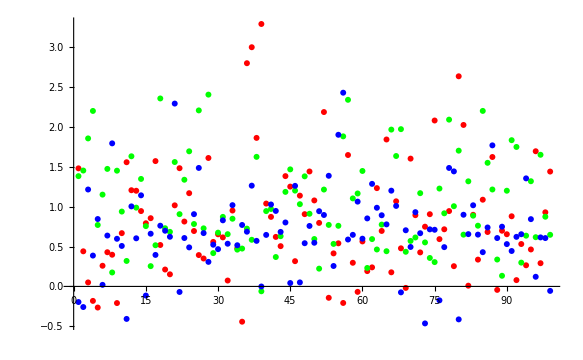

{RGB,RGB,RG,R,RG,GB,R,RGB,RG,G,RGB,R,RG,RGB,GB,G,RG,RG,RG,RG,RGB,RGB,RG,RG,G,RGB,RGB,NaN,G,RG,G,RG,RGB,G,RG,G,GB,RG,GB,RG,GB,G,RG,RG,RGB,RGB,RGB,RG,G,GB,G,GB,RG,RGB,G,RB,NaN,G,G,NaN,RG,RGB,RG,RG,G,RGB,RG,B,RGB,RG,G,RG,GB,RG,RG,RGB,RGB,RGB,RGB,RGB,RGB,RGB,G,G,B,R,GB,RGB,G,G,G,R,RG,RGB,GB,GB,RG,RG,GB}

{{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-}}

```mathematica
ListPlot[tempDD[[All,2;;All]], PlotStyle->{Red, Green, Blue}   ]
dataframePFDD[[2;;y,6]]
dataframePFDD[[2;;y,3;;5]]
```

```mathematica
Sort[{"RGB","RGB","RG","R","RG","GB","R","RGB","RG"}]
```

{GB,R,R,RG,RG,RG,RGB,RGB,RGB}

```mathematica
temp = dataframePFDD[[2;;8]]
```

{{1,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.13304,5.30793,0.220131,0.201389,9.00269,5.50548,5.28965,0.209431,0.445167,6.94142,7.21902,2.13221,0.42265,0.569894,2.02823,0.331404,0.132991,21,55,stdevdisk,stdevdonut,0.268484,0.193628,21,55,stdevdisk,stdevdonut,0.00433113,0.428538,74,89,stdevdisk,stdevdonut},{2,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.88285,3.52869,0.183503,0.216098,7.89203,5.75317,5.79664,0.166608,0.466102,9.77707,4.48225,6.95293,0.618034,0.747127,3.31035,0.124926,0.136506,43,58,stdevdisk,stdevdonut,0.191777,0.320919,21,50,stdevdisk,stdevdonut,0.0615259,0.483327,21,36,stdevdisk,stdevdonut},{3,1,-Graphics-,-Graphics-,-Graphics-,RG,6.68493,4.37179,0.143913,0.248402,11.2867,5.50861,5.83661,0.0451363,0.249073,9.67536,NaN,NaN,NaN,NaN,NaN,0.156028,0.185811,43,58,stdevdisk,stdevdonut,0.25523,0.222231,21,50,stdevdisk,stdevdonut,0.0838883,0.236215,21,60,stdevdisk,stdevdonut},{4,1,-Graphics-,-Graphics-,-Graphics-,R,7.00131,3.40263,0.151497,0.505364,10.8688,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,0.071092,0.312257,62,71,stdevdisk,stdevdonut,0.25242,0.309281,21,60,stdevdisk,stdevdonut,-0.034076,0.18599,21,60,stdevdisk,stdevdonut},{5,1,-Graphics-,-Graphics-,-Graphics-,RG,5.23909,4.45246,0.0741799,0.686488,5.2511,5.33734,5.8227,0.280592,0.386755,5.93555,NaN,NaN,NaN,NaN,NaN,0.0911278,0.368166,43,70,stdevdisk,stdevdonut,0.199908,0.261638,21,55,stdevdisk,stdevdonut,0.0448341,0.38256,21,60,stdevdisk,stdevdonut},{6,1,-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.95321,5.92684,0.,0.348135,2.46555,7.99987,6.03195,0.,0.595193,3.18096,-0.0703646,0.333062,21,60,stdevdisk,stdevdonut,0.115905,0.242785,21,50,stdevdisk,stdevdonut,0.12961,0.36308,21,37,stdevdisk,stdevdonut},{7,1,-Graphics-,-Graphics-,-Graphics-,R,6.57499,3.63084,0.489939,0.388281,10.4711,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,0.154399,0.184328,43,58,stdevdisk,stdevdonut,0.193153,0.44738,21,60,stdevdisk,stdevdonut,0.0130772,0.412192,21,60,stdevdisk,stdevdonut}}

```mathematica
dataframePFDD[[1;;50]]
```

### DONT TRY TO WORK ON DD... Just try to build a hand checker for the spots....

```mathematica
dataframePFDD[[1;;10]]
```

{{Frame#,Spot#,RCrop,GCrop,BCrop,Color Classifier,X_IntensityCentroid_R,Y_IntensityCentroid_R,Elongation_R,MinIntensity_R,TotalIntensity_R,X_IntensityCentroid_G,Y_IntensityCentroid_G,Elongation_G,MinIntensity_G,TotalIntensity_G,X_IntensityCentroid_B,Y_IntensityCentroid_B,Elongation_B,MinIntensity_B,TotalIntensity_B,Rmeanintensitydisk,Rmeanintensitydonut,RpixsizeDisk,RpixsizeDonut,RstdevDisk,RstdevDonut,Gmeanintensitydisk,Gmeanintensitydonut,GpixsizeDisk,GpixsizeDonut,GstdevDis,GstdevDonut,Bmeanintensitydisk,Bmeanintensitydonut,BpixsizeDisk,BpixsizeDonut,BstdevDisk,BstdevDonut},{1,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.13304,5.30793,0.220131,0.201389,9.00269,5.50548,5.28965,0.209431,0.445167,6.94142,7.21902,2.13221,0.42265,0.569894,2.02823,0.183342,0.123722,21,89,stdevdisk,stdevdonut,0.236884,0.171157,21,89,stdevdisk,stdevdonut,-0.0461121,0.235548,150,198,stdevdisk,stdevdonut},{2,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.88285,3.52869,0.183503,0.216098,7.89203,5.75317,5.79664,0.166608,0.466102,9.77707,4.48225,6.95293,0.618034,0.747127,3.31035,0.0288998,0.0655743,108,172,stdevdisk,stdevdonut,0.301291,0.207168,21,112,stdevdisk,stdevdonut,-0.0743247,0.287288,48,112,stdevdisk,stdevdonut},{3,1,-Graphics-,-Graphics-,-Graphics-,RG,6.68493,4.37179,0.143913,0.248402,11.2867,5.50861,5.83661,0.0451363,0.249073,9.67536,NaN,NaN,NaN,NaN,NaN,0.0050419,0.100267,108,172,stdevdisk,stdevdonut,0.292888,0.15768,21,112,stdevdisk,stdevdonut,0.175671,0.144432,21,140,stdevdisk,stdevdonut},{4,1,-Graphics-,-Graphics-,-Graphics-,R,7.00131,3.40263,0.151497,0.505364,10.8688,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,-0.0308685,0.170068,128,186,stdevdisk,stdevdonut,0.38629,0.17541,21,140,stdevdisk,stdevdonut,0.0424041,0.10951,21,140,stdevdisk,stdevdonut},{5,1,-Graphics-,-Graphics-,-Graphics-,RG,5.23909,4.45246,0.0741799,0.686488,5.2511,5.33734,5.8227,0.280592,0.386755,5.93555,NaN,NaN,NaN,NaN,NaN,-0.0698641,0.263819,48,87,stdevdisk,stdevdonut,0.169245,0.219498,21,89,stdevdisk,stdevdonut,0.195848,0.231546,21,140,stdevdisk,stdevdonut},{6,1,-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.95321,5.92684,0.,0.348135,2.46555,7.99987,6.03195,0.,0.595193,3.18096,0.0541058,0.208592,21,140,stdevdisk,stdevdonut,0.188506,0.163612,21,112,stdevdisk,stdevdonut,0.00418771,0.211852,51,151,stdevdisk,stdevdonut},{7,1,-Graphics-,-Graphics-,-Graphics-,R,6.57499,3.63084,0.489939,0.388281,10.4711,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,0.0369682,0.0861343,108,172,stdevdisk,stdevdonut,0.381726,0.258807,21,140,stdevdisk,stdevdonut,0.165691,0.259578,21,140,stdevdisk,stdevdonut},{8,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.02103,3.94743,0.25838,0.296773,7.86473,5.4749,5.45819,1.11022×10^-16,0.574578,7.06151,6.07109,4.85674,0.12822,0.17673,8.1546,0.0421617,0.106003,48,102,stdevdisk,stdevdonut,0.0738598,0.421486,21,70,stdevdisk,stdevdonut,0.221922,0.123602,21,89,stdevdisk,stdevdonut},{9,1,-Graphics-,-Graphics-,-Graphics-,RG,7.33237,5.45384,0.209431,0.327565,5.91853,5.58946,5.68218,0.209431,0.341268,5.11148,NaN,NaN,NaN,NaN,NaN,-0.0189824,0.0909961,81,162,stdevdisk,stdevdonut,0.242732,0.167105,21,112,stdevdisk,stdevdonut,0.15073,0.2521,21,140,stdevdisk,stdevdonut}}

```mathematica
dataframePFDD[[1;;2]]
dataframePFDD[[1,36;;37]]
```

{{Frame#,Spot#,RCrop,GCrop,BCrop,Color Classifier,X_IntensityCentroid_R,Y_IntensityCentroid_R,Elongation_R,MinIntensity_R,TotalIntensity_R,X_IntensityCentroid_G,Y_IntensityCentroid_G,Elongation_G,MinIntensity_G,TotalIntensity_G,X_IntensityCentroid_B,Y_IntensityCentroid_B,Elongation_B,MinIntensity_B,TotalIntensity_B,Rmeanintensitydisk,Rmeanintensitydonut,RpixsizeDisk,RpixsizeDonut,RstdevDisk,RstdevDonut,Gmeanintensitydisk,Gmeanintensitydonut,GpixsizeDisk,GpixsizeDonut,GstdevDis,GstdevDonut,Bmeanintensitydisk,Bmeanintensitydonut,BpixsizeDisk,BpixsizeDonut,BstdevDisk,BstdevDonut},{1,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.13304,5.30793,0.220131,0.201389,9.00269,5.50548,5.28965,0.209431,0.445167,6.94142,7.21902,2.13221,0.42265,0.569894,2.02823,0.183342,0.123722,21,89,stdevdisk,stdevdonut,0.236884,0.171157,21,89,stdevdisk,stdevdonut,-0.0461121,0.235548,150,198,stdevdisk,stdevdonut}}

{BpixsizeDisk,BpixsizeDonut}

```mathematica
pad2 =myPadSize;
myTfFunc=myTF ;
```

```mathematica
(*pad2 =myPad;
Manipulate[ 
tempCenter=Ceiling@dataframePFDD[[frame,trackN]];
tftempCenter=Ceiling@myTfFunc@dataframePFDD[[frame,trackN]];
{tempRed,tempGreen,tempBlue}=
{ImageAdjust@ImageTrim[myColMovie⟦1,frame⟧,{tempCenter-pad2,tempCenter+pad2-0.1}],
ImageAdjust@ImageTrim[myColMovie⟦2,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}],
ImageAdjust@ImageTrim[myColMovie⟦3,frame⟧,{tftempCenter-pad2,tftempCenter+pad2-0.1}]};
myCell=Show[ myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},
If[channel==1,thred,If[channel==2,thgreen,thblue]]     
]&,
Graphics[{RGBColor[1, 0.04, 0.88],Circle[#,7]& @(dataframePFDD ⟦frame,trackN⟧) 
}]];
{tempRed,tempGreen,tempBlue,myCell},
{{channel,2},{1,2,3}},{frame,1,Length@dataframePFDD,1},{trackN,1,Length@dataframePFDD[[frame]],1}
]
```

```mathematica
myMovieFileName
```

/Volumes/BITTY/_Mathematica_session_copy/BG_MAX_Cell05.tif

```mathematica
myColMovie=Import[myMovieFileName]//Partition[#,3]&//Transpose;
```

```mathematica
myColMovieRunAv = myColMovie ;
```

```mathematica
(*Manipulate just the crops : 
*)
Manipulate[ 
{  dataframePFDD[[trackN, 3;;5]] },
{trackN,1,Length@dataframePFDD,1}
]
```

```mathematica
dataframePFDDlocs[[1;;2]]
```

{{Frame#,Spot#,RCrop,GCrop,BCrop,Color Classifier,X_IntensityCentroid_R,Y_IntensityCentroid_R,Elongation_R,MinIntensity_R,TotalIntensity_R,X_IntensityCentroid_G,Y_IntensityCentroid_G,Elongation_G,MinIntensity_G,TotalIntensity_G,X_IntensityCentroid_B,Y_IntensityCentroid_B,Elongation_B,MinIntensity_B,TotalIntensity_B,Rmeanintensitydisk,Rmeanintensitydonut,RpixsizeDisk,RpixsizeDonut,RstdevDisk,RstdevDonut,Gmeanintensitydisk,Gmeanintensitydonut,GpixsizeDisk,GpixsizeDonut,GstdevDis,GstdevDonut,Bmeanintensitydisk,Bmeanintensitydonut,BpixsizeDisk,BpixsizeDonut,BstdevDisk,BstdevDonut,XLocation,YLocation},{1,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.13304,5.30793,0.220131,0.201389,9.00269,5.50548,5.28965,0.209431,0.445167,6.94142,7.21902,2.13221,0.42265,0.569894,2.02823,0.183342,0.123722,21,89,stdevdisk,stdevdonut,0.236884,0.171157,21,89,stdevdisk,stdevdonut,-0.0461121,0.235548,150,198,stdevdisk,stdevdonut,393.564,411.185}}

```mathematica
trackN = 2;dataframePFDDlocs ⟦trackN, 40;;41⟧
tempCenter=Ceiling@dataframePFDDlocs[[trackN,40;;41]]
tftempCenter=Ceiling@myTfFunc@dataframePFDDlocs[[trackN,40;;41]]
```

{393.564,411.185}

{394,412}

{396,414}

```mathematica
myColMovieRunAv[[1]]//Length
```

55

```mathematica
tempCenter=Ceiling@dataframePFDDlocs[[trackN,40;;41]]
tftempCenter=Ceiling@myTfFunc@dataframePFDDlocs[[trackN,40;;41 ]]
```

{394,412}

{396,414}

Manipulate: Movie shows the spot location over time...

```mathematica
Manipulate[ 
tempCenter=Ceiling@dataframePFDDlocs[[trackN,40;;41]];
tftempCenter=Ceiling@myTfFunc@dataframePFDDlocs[[trackN,40;;41 ]];
{tempCenter,tftempCenter},
{trackN,2,Length@dataframePFDDlocs[[1]],1}
]
```

```mathematica
(*Cell over time *) 
Manipulate[ 
myCell=Show[ myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},
If[channel==1,thred,If[channel==2,thgreen,thblue]]     
]&  ],
{{channel,2},{1,2,3}},{frame,1,Length@myColMovieRunAv[[1]],1}
]
```

Manipulate: Goes thru movie frame by frame to cycle thru all spots at that frame ....

```mathematica
Manipulate[
tempSpotList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[2]] &][[frame]]   ;
tempCenter=Ceiling@tempSpotList[[trackN,40;;41  ]];
(*tftempCenter=Ceiling@myTfFunc@tempSpotList[[trackN, 40;;41  ]];*)

myCell=Show[ myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},
If[channel==1,thred,If[channel==2,thgreen,thblue]]     
]&  ,
Graphics[{RGBColor[1, 0.04, 0.88],Circle[#,7]& @(tempCenter) 
}]];

{myCell, tempCenter},
{{channel,2},{1,2,3}},{frame,1,Length@myColMovieRunAv[[1]],1},{trackN,1,Length@tempSpotList,1}
]
```

Manipulate just the crops :

```mathematica
Manipulate[ 
{  dataframePFDD[[trackN, 3;;5]] },
{trackN,1,Length@dataframePFDD,1}
]
```

Manipulate just the crops :

```mathematica
(*The RGB of all spots at each frame, over time*)
Manipulate[
tempSpotList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[2]] &][[frame]];
tempSpotList[[All,3;;5]]  ,
{{channel,2},{1,2,3}},{frame,1,Length@myColMovieRunAv[[1]],1},{trackN,1,Length@tempSpotList,1}
]
```

Manipulate just the crops gathered by category :

```mathematica
{"RGB", "RG", "R", "GB", "G", "NaN", "RB", "B"}
```

{RGB,RG,R,GB,G,NaN,RB,B}

```mathematica
tempSpotList[[2,All,6]]
```

```mathematica
tempSpotList = GatherBy[dataframePFDDlocs,  #[[6]] &];
```

```mathematica
tempColorList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[6]] &];
Dimensions@tempColorList
```

{8}

```mathematica
(*The RGB of all spots at each frame, over time*)
Manipulate[
tempColorList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[6]] &];
{{"RGB","RG","R","GB","G","NaN","RB","B"}[[color]],
tempColorList[[color, All,3;;5]] } ,
{color,1,Length@tempColorList,1}
]
```

```mathematica
list = {{"stuff"}, {"stuff"}}
```

{{stuff},{stuff}}

```mathematica
(*Buttoning of all spots at each frame, over time*)
Manipulate[
tempColorList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[6]] &];
{{"RGB","RG","R","GB","G","NaN","RB","B"}[[color]],
Button[#, Append[list,#]]&/@tempColorList[[color, All,3;;5]] } ,
{color,1,Length@tempColorList,1}
]
```

```mathematica
list
```

{{stuff},{stuff}}

```mathematica
Append[list,{-Graphics-,-Graphics-,-Graphics-}]
```

{{stuff},{stuff},{-Graphics-,-Graphics-,-Graphics-}}

Manipulate: cycling thru movies and spots PLUS crops...

```mathematica
Manipulate[
tempSpotList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[2]] &][[frame]]   ;
tempCenter=Ceiling@tempSpotList[[trackN,40;;41  ]];
tempCall=tempSpotList[[trackN,6  ]];

myCell=Show[ myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},
If[channel==1,thred,If[channel==2,thgreen,thblue]]     
]&  ,
Graphics[{RGBColor[1, 0.04, 0.88],Circle[#,7]& @(tempCenter) 
}]];
myCell2 = tempSpotList[[All,3;;5]][[trackN]]  ;
{myCell, Column[{tempCenter,tempCall,myCell2}]},
{{channel,2},{1,2,3}},{frame,1,Length@myColMovieRunAv[[1]],1},{trackN,1,Length@tempSpotList,1}
]
```

Manipulate: cycling thru movies and spots MINUS crops...

```mathematica
{{"RGB","RG","R","GB","G","NaN","RB","B"}
```

```mathematica
colorList= {Gray, Yellow, Red, Cyan, Black, Purple, Blue}
```

{GrayLevel[0.5],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 1],GrayLevel[0],RGBColor[0.5, 0, 0.5],RGBColor[0, 0, 1]}

Manipulate: each spot color coded one at a time per frame:

```mathematica
Manipulate[
tempSpotList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[2]] &][[frame]]   ;
tempCenter=Ceiling@tempSpotList[[trackN,40;;41  ]];
tempCall=tempSpotList[[trackN,6  ]];
hue = Which[ tempCall=="RGB",White,  tempCall=="RG",Yellow,   tempCall=="R",Red,   tempCall=="GB",Cyan,  tempCall=="G",Green,   tempCall=="NaN",Black,   tempCall=="RB",Lighter[Purple],   tempCall=="B",Blue  ,tempCall ≠ "NaN",Black ];

myCell=Show[ myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},
If[channel==1,thred,If[channel==2,thgreen,thblue]]     
]&  ,
Graphics[{hue,Circle[#,7]& @(tempCenter) 
}]];

{myCell, tempCall , tempCenter},
{{channel,2},{1,2,3}},{frame,1,Length@myColMovieRunAv[[1]],1},{trackN,1,Length@tempSpotList,1}
]
```

Manipulate:, all color calls at the same time, per frame

```mathematica
Manipulate[
tempSpotList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[2]] &][[frame]]   ;
tempCenters=Ceiling/@tempSpotList[[All,40;;41  ]];
tempCalls=tempSpotList[[All,6  ]];
hue = Table[Which[ tempCalls[[trackN]]=="RGB",White,  tempCalls[[trackN]]=="RG",Yellow,   tempCalls[[trackN]]=="R",Red,   tempCalls[[trackN]]=="GB",Cyan,  tempCalls[[trackN]]=="G",Green,   tempCalls[[trackN]]=="NaN",Black,   tempCalls[[trackN]]=="RB",Lighter[Purple],   tempCalls[[trackN]]=="B",Blue  ,tempCalls [[trackN]]≠ "NaN",Black ],{trackN,1,Length@tempCalls}];

myCell=Show[ myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},
If[channel==1,thred,If[channel==2,thgreen,thblue]]     
]&  ,
Table[Graphics[{hue[[trackN]],Circle[#,7]& @(tempCenters[[trackN]]) 
}],{trackN,1,Length@tempCalls}]];

{myCell, tempCalls },
{{channel,2},{1,2,3}},{frame,1,Length@myColMovieRunAv[[1]],1}(*{trackN,1,Length@tempSpotList,1}*)
]
```

Manipulate: cycling thru frames of movies with all classified spots showing, MINUS crops...

```mathematica
tempSpotList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[2]] &][[frame]]
```

{{1,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.13304,5.30793,0.220131,0.201389,9.00269,5.50548,5.28965,0.209431,0.445167,6.94142,7.21902,2.13221,0.42265,0.569894,2.02823,0.183342,0.123722,21,89,stdevdisk,stdevdonut,0.236884,0.171157,21,89,stdevdisk,stdevdonut,-0.0461121,0.235548,150,198,stdevdisk,stdevdonut,393.564,411.185},{2,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.88285,3.52869,0.183503,0.216098,7.89203,5.75317,5.79664,0.166608,0.466102,9.77707,4.48225,6.95293,0.618034,0.747127,3.31035,0.0288998,0.0655743,108,172,stdevdisk,stdevdonut,0.301291,0.207168,21,112,stdevdisk,stdevdonut,-0.0743247,0.287288,48,112,stdevdisk,stdevdonut,270.576,396.896},{3,1,-Graphics-,-Graphics-,-Graphics-,RG,6.68493,4.37179,0.143913,0.248402,11.2867,5.50861,5.83661,0.0451363,0.249073,9.67536,NaN,NaN,NaN,NaN,NaN,0.0050419,0.100267,108,172,stdevdisk,stdevdonut,0.292888,0.15768,21,112,stdevdisk,stdevdonut,0.175671,0.144432,21,140,stdevdisk,stdevdonut,344.603,375.997},{4,1,-Graphics-,-Graphics-,-Graphics-,R,7.00131,3.40263,0.151497,0.505364,10.8688,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,-0.0308685,0.170068,128,186,stdevdisk,stdevdonut,0.38629,0.17541,21,140,stdevdisk,stdevdonut,0.0424041,0.10951,21,140,stdevdisk,stdevdonut,319.459,340.007},{5,1,-Graphics-,-Graphics-,-Graphics-,RG,5.23909,4.45246,0.0741799,0.686488,5.2511,5.33734,5.8227,0.280592,0.386755,5.93555,NaN,NaN,NaN,NaN,NaN,-0.0698641,0.263819,48,87,stdevdisk,stdevdonut,0.169245,0.219498,21,89,stdevdisk,stdevdonut,0.195848,0.231546,21,140,stdevdisk,stdevdonut,217.003,335.617},{6,1,-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,5.95321,5.92684,0.,0.348135,2.46555,7.99987,6.03195,0.,0.595193,3.18096,0.0541058,0.208592,21,140,stdevdisk,stdevdonut,0.188506,0.163612,21,112,stdevdisk,stdevdonut,0.00418771,0.211852,51,151,stdevdisk,stdevdonut,212.859,310.919},{7,1,-Graphics-,-Graphics-,-Graphics-,R,6.57499,3.63084,0.489939,0.388281,10.4711,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,0.0369682,0.0861343,108,172,stdevdisk,stdevdonut,0.381726,0.258807,21,140,stdevdisk,stdevdonut,0.165691,0.259578,21,140,stdevdisk,stdevdonut,114.846,193.678},{8,1,-Graphics-,-Graphics-,-Graphics-,RGB,6.02103,3.94743,0.25838,0.296773,7.86473,5.4749,5.45819,1.11022×10^-16,0.574578,7.06151,6.07109,4.85674,0.12822,0.17673,8.1546,0.0421617,0.106003,48,102,stdevdisk,stdevdonut,0.0738598,0.421486,21,70,stdevdisk,stdevdonut,0.221922,0.123602,21,89,stdevdisk,stdevdonut,76.4857,192.476},{9,1,-Graphics-,-Graphics-,-Graphics-,RG,7.33237,5.45384,0.209431,0.327565,5.91853,5.58946,5.68218,0.209431,0.341268,5.11148,NaN,NaN,NaN,NaN,NaN,-0.0189824,0.0909961,81,162,stdevdisk,stdevdonut,0.242732,0.167105,21,112,stdevdisk,stdevdonut,0.15073,0.2521,21,140,stdevdisk,stdevdonut,77.4947,171.798},{10,1,-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,6.28568,6.14591,0.362328,0.401663,10.6871,NaN,NaN,NaN,NaN,NaN,0.181984,0.272172,21,140,stdevdisk,stdevdonut,0.276182,0.293992,21,112,stdevdisk,stdevdonut,0.128559,0.253112,21,140,stdevdisk,stdevdonut,107.507,170.726},{11,1,-Graphics-,-Graphics-,-Graphics-,RGB,5.97995,4.65652,0.12235,0.209628,11.983,5.363,5.32642,0.03705,0.389151,7.2761,5.31343,4.33274,0.591752,0.627375,3.36265,0.274136,0.175881,21,89,stdevdisk,stdevdonut,0.075006,0.234557,21,70,stdevdisk,stdevdonut,-0.122888,0.30148,48,87,stdevdisk,stdevdonut,85.5041,159.395},{12,1,-Graphics-,-Graphics-,-Graphics-,R,6.43751,5.14701,0.451369,0.342229,12.4415,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,NaN,0.19414,0.160806,21,89,stdevdisk,stdevdonut,0.422333,0.258581,21,140,stdevdisk,stdevdonut,0.225866,0.224866,21,140,stdevdisk,stdevdonut,117.87,160.046},{13,1,-Graphics-,-Graphics-,-Graphics-,RG,4.90157,5.0515,0.148009,0.341283,7.47926,5.66905,5.6116,0.169051,0.350652,8.44588,NaN,NaN,NaN,NaN,NaN,0.196028,0.163287,21,70,stdevdisk,stdevdonut,0.303677,0.307106,21,112,stdevdisk,stdevdonut,0.145429,0.240783,21,140,stdevdisk,stdevdonut,188.614,153.614},{14,1,-Graphics-,-Graphics-,-Graphics-,RGB,5.0024,5.12477,0.12492,0.276677,8.98869,5.6895,5.97553,0.0209569,0.405585,9.69009,4.81193,6.00717,0.0209569,0.324331,7.30857,0.176619,0.186785,21,70,stdevdisk,stdevdonut,0.274155,0.203228,21,112,stdevdisk,stdevdonut,0.182781,0.159872,21,89,stdevdisk,stdevdonut,72.422,147.87},{15,1,-Graphics-,-Graphics-,-Graphics-,GB,NaN,NaN,NaN,NaN,NaN,4.92051,5.77227,0.435168,0.373114,21.6836,3.96547,6.96547,0.646447,0.683131,1.46763,0.202819,0.25581,21,140,stdevdisk,stdevdonut,0.253601,0.33507,21,89,stdevdisk,stdevdonut,-0.0247325,0.216065,48,112,stdevdisk,stdevdonut,233.094,132.559},{16,1,-Graphics-,-Graphics-,-Graphics-,G,NaN,NaN,NaN,NaN,NaN,5.43381,5.3309,0.209431,0.469215,5.72079,NaN,NaN,NaN,NaN,NaN,0.146454,0.171025,21,140,stdevdisk,stdevdonut,0.0664997,0.261127,21,70,stdevdisk,stdevdonut,0.188554,0.285054,21,140,stdevdisk,stdevdonut,199.4,128.356},{17,1,-Graphics-,-Graphics-,-Graphics-,RG,7.58754,6.88481,0.294233,0.351461,6.34249,5.38446,5.46472,0.161022,0.264698,11.3384,NaN,NaN,NaN,NaN,NaN,0.227837,0.144851,21,135,stdevdisk,stdevdonut,0.122128,0.236256,21,70,stdevdisk,stdevdonut,0.108666,0.274794,21,140,stdevdisk,stdevdonut,123.258,118.416},{18,1,-Graphics-,-Graphics-,-Graphics-,RG,8.06921,5.93208,0.,0.320912,6.95096,5.74198,6.10077,0.220131,0.246357,9.22182,NaN,NaN,NaN,NaN,NaN,0.0503796,0.0969044,51,151,stdevdisk,stdevdonut,0.280811,0.119047,21,112,stdevdisk,stdevdonut,0.140605,0.18447,21,140,stdevdisk,stdevdonut,253.701,117.976},{19,1,-Graphics-,-Graphics-,-Graphics-,RG,7.89925,5.24733,0.148009,0.265843,7.21154,5.98527,5.01204,0.25838,0.346136,7.08945,NaN,NaN,NaN,NaN,NaN,0.0128502,0.0605635,81,157,stdevdisk,stdevdonut,0.13359,0.18293,21,89,stdevdisk,stdevdonut,0.128846,0.18437,21,140,stdevdisk,stdevdonut,216.776,114.139},{20,1,-Graphics-,-Graphics-,-Graphics-,RG,5.72245,3.57845,0.651822,0.251087,13.402,5.47255,6.00803,0.313771,0.373571,8.81813,NaN,NaN,NaN,NaN,NaN,0.023527,0.154657,48,102,stdevdisk,stdevdonut,0.161398,0.235675,21,89,stdevdisk,stdevdonut,0.124619,0.199974,21,140,stdevdisk,stdevdonut,229.397,111.98},{21,1,-Graphics-,-Graphics-,-Graphics-,RGB,4.98723,4.86635,0.12492,0.229389,9.67945,5.83677,5.87264,0.148009,0.320806,7.68981,4.91963,5.53472,0.183503,0.194842,8.00963,0.190286,0.186985,21,70,stdevdisk,stdevdonut,0.24984,0.160043,21,112,stdevdisk,stdevdonut,0.243688,0.106201,21,89,stdevdisk,stdevdonut,250.89,99.6036},{22,1,-Graphics-,-Graphics-,-Graphics-,RGB,5.52003,4.04423,0.183503,0.257694,7.99855,5.03509,5.787,0.0209569,0.312856,8.9005,4.6346,4.20116,0.280592,0.405859,6.77182,0.0858159,0.0578386,48,102,stdevdisk,stdevdonut,0.197963,0.218289,21,89,stdevdisk,stdevdonut,-0.0135585,0.195122,48,87,stdevdisk,stdevdonut,258.017,79.7863}}

```mathematica
Manipulate[
tempSpotList = GatherBy[dataframePFDDlocs[[2;;All]],  #[[2]] &][[frame]]   ;
tempCenter=Ceiling@tempSpotList[[trackN,40;;41  ]];
(*tftempCenter=Ceiling@myTfFunc@tempSpotList[[trackN, 40;;41  ]];*)

myCell=Show[ myColMovieRunAv⟦channel,frame⟧//ImageAdjust[#,{0,0,1},
If[channel==1,thred,If[channel==2,thgreen,thblue]]     
]&  ,
Graphics[{RGBColor[1, 0.04, 0.88],Circle[#,7]& @(tempCenter) 
}]];

{myCell, tempCenter},
{{channel,2},{1,2,3}},{frame,1,Length@myColMovieRunAv[[1]],1},{trackN,1,Length@tempSpotList,1}
]
```

### Unused...

```mathematica
(*NOT used, ...*)Table[
Select [dataframePFDDlocs[[All,2]]==frame, 
{Ceiling@dataframePFDDlocs[[trackN,40;;41  ]],
Ceiling@myTfFunc@dataframePFDDlocs[[trackN, 40;;41  ]] }],
{frame,1,10}]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
(*NOT used...*)Table[If [dataframePFDDlocs[[spot,2]]==frame, 
dataframePFDDlocs[[spot,40;;41]] ],{spot, 1, Length@dataframePFDDlocs}]
```